## Lesson

Import from an external source:

```mathematica
Import["http://wikipedia.org","Images"]
```

{-Graphics-}

Create a new connection with a Twitter account:

```mathematica
tw=ServiceConnect["Twitter","New"]
```

ServiceObject[…]

Search the web for images:

```mathematica
WebImageSearch["colourful birds"]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

Access data from the Wolfram data repository:

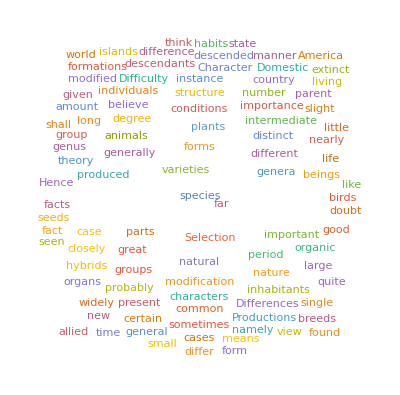

```mathematica
WordCloud[ResourceData["On the Origin of Species"]]
```

Send emails:

```mathematica
SendMail["tp873@bath.ac.uk", {"Wolf", "Here's a wolf...", -Graphics-}]
```

Failure[PlanRestrictionFailure]

Export to the cloud:

```mathematica
CloudExport[Graphics[Circle[]],"PDF"]
```

CloudObject[https://www.wolframcloud.com/obj/2ba153ea-e414-46c0-94de-357fa0782de5]

Export to file:

```mathematica
Export["primepowers.xls",Table[Prime[m]^n,{m,10},{n,4}]]
```

primepowers.xls

Import from file:

```mathematica
Import["primepowers.xls"]
```

{{{2.,4.,8.,16.},{3.,9.,27.,81.},{5.,25.,125.,625.},{7.,49.,343.,2401.},{11.,121.,1331.,14641.},{13.,169.,2197.,28561.},{17.,289.,4913.,83521.},{19.,361.,6859.,130321.},{23.,529.,12167.,279841.},{29.,841.,24389.,707281.}}}

Send object to be 3D printed:

```mathematica
Printout3D[Graphics3D[Sphere[RandomReal[5,{30,3}]]],"Sculpteo"]
```

## Questions

Q1. Import the images from http://google.com.

```mathematica
Import["https://www.google.com/","Images"]
```

{-Graphics-}

Q2. Make an image collage of disks with the dominant colours from images on http://google.com.

```mathematica
ImageCollage[Graphics[Style[Disk[],#]]&/@Flatten[DominantColors[Import["https://www.google.com/","Images"]]]]
```

-Graphics-

Q3. Make a word cloud of the text on http://bbc.co.uk.

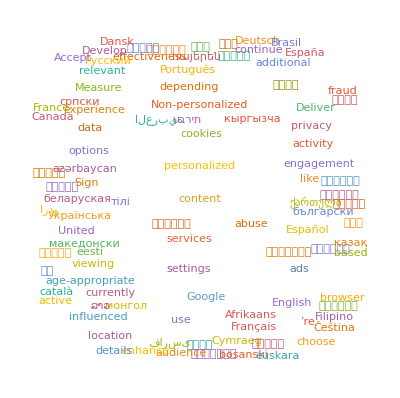

```mathematica
WordCloud[Import["https://www.google.com/"]]
```

Q4. Make an image collage of the images on http://nps.gov.

```mathematica
ImageCollage[Import["https://www.nps.gov/","Images"]]
```

Import::htmlimg: Some images could not be imported.

-Graphics-

Q5. Use ImageInstanceQ to find pictures on https://en.wikipedia.org/wiki/Ostrich that are of birds.

```mathematica
Select[Import["https://en.wikipedia.org/wiki/Ostrich","Images"],ImageInstanceQ[#,Entity["Species","Class:Aves"]]&]
```

Import::htmlimg: Some images could not be imported.

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

Q6. Use TextCases with “Country” to find instances of country names on http://nato.int, and make a word cloud of them.

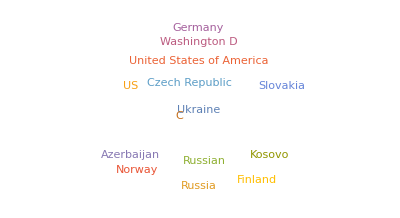

```mathematica
WordCloud[TextCases[Import["http://nato.int"],"Country"]]
```

Q7. Find the number of links on https://en.wikipedia.org.

```mathematica
Length[Import["https://en.wikipedia.org","Hyperlinks"]]
```

325

Q8. Send yourself mail with a map of your current location.

```mathematica
SendMail[GeoGraphics[Here]]
```

SendMail::cloudrelay: SendMail has relayed your message through the Wolfram Cloud.  A local SMTP server has not been configured. These settings can be defined through Preferences > Internet & Mail > Mail Settings in the notebook front end.

Failure[PlanRestrictionFailure]

Q9. Send yourself mail with an icon of the current phase of the moon.

```mathematica
SendMail[MoonPhase[Now,"Icon"]]
```